```mathematica
m=Table[0,{i,1,9}];
m[[1]]=Import["output"<>ToString[1]<>".dat"]
```

{{8464,-0.0000215354},{9464,-6.07239×10^-8},{10464,-1.73008×10^-8},{11464,-9.89551×10^-9},{12464,-1.16068×10^-8},{13464,-4.20067×10^-9},{14464,-2.11322×10^-9},{15464,-2.11645×10^-9},{16464,-1.79711×10^-9},{17464,-1.31852×10^-9},{18464,-1.14589×10^-9},{19464,-1.17309×10^-9},{20464,-1.29424×10^-9},{21464,-6.48038×10^-10},{22464,-1.55051×10^-9}}

```mathematica
forPlot=Import["output1.dat"];
Length[forPlot]
(*For[i=1, i<5,i++,m[[i]]=Import["output"<>ToString[i]<>".dat"]];*)
```

20

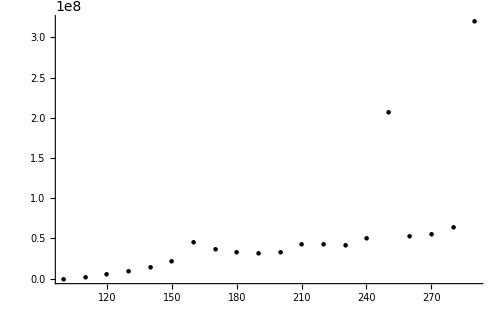

```mathematica
ListPlot[forPlot,PlotRange->All,PlotStyle->Black,PlotMarkers->{Automatic,6},AxesOrigin->{0,0}]
```

```mathematica
finalPlot=Table[{m[[1,k,1]],
(m[[1,k,2]]+m[[2,k,2]]+m[[3,k,2]]+m[[4,k,2]])
},{k,1,Length[m[[1]]]}]
```

{{8464,-0.0000386646+-inf},{9464,-0.000175674},{10464,0.0000304996},{11464,-6.53187×10^-6},{12464,-8.06845×10^-8},{13464,-2.74426×10^-8},{14464,-7.32566×10^-7},{15464,-1.80983×10^-9},{16464,-9.06076×10^-9},{17464,-3.38194×10^-8},{18464,-1.50383×10^-10},{19464,-4.12055×10^-8},{20464,4.13604×10^-8},{21464,8.24943×10^-10},{22464,-1.41831×10^-9}}

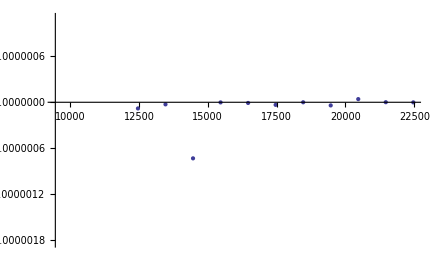

```mathematica
ListPlot[finalPlot]
```